```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["pdfLaTeX" -> "/usr/local/bin/pdflatex"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color}"}]
```

## Energy control

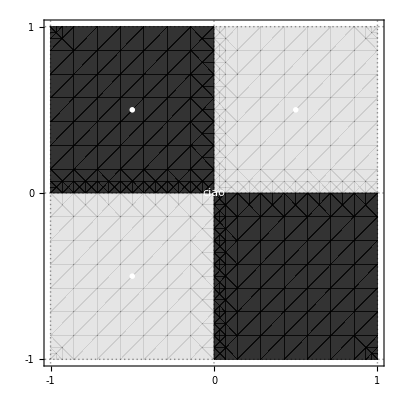

```mathematica
energyControl = ContourPlot[x*y, {x, -1, 1}, {y, -1, 1},
Contours->1,
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotRange->{1, -1},
FrameLabel ->{MaTeX[TeXForm[θ],Magnification->2],MaTeX[ "E",Magnification->2]},
FrameTicks->{{0, -1, 1}, {0, -1, 1}},
GridLines->{{0, -1, 1}, {0, -1, 1}},
Epilog->{
White,
Text[MaTeX["+a_{max}",Magnification->2], {.5, .5}],Text[MaTeX["+a_{max}",Magnification->2], {-.5, -.5}],
Text[MaTeX["-a_{max}",Magnification->2], {-.5, .5}],
Text[MaTeX["-a_{max}",Magnification->2], {-.5, .5}]
}
]
```

```mathematica
Show[energyControl,Background->Black]
```

```mathematica
Export[NotebookDirectory[]<>"../energy-control.pdf",energyControl,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf

## Cogging Torque

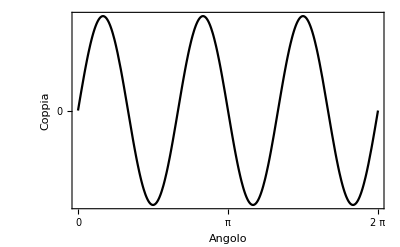

```mathematica
coggingTorque = Plot[Sin[3*x], {x, 0, 2Pi},
PlotTheme->{"Monochrome", "SerifLabels", "FrameGrid"},
PlotLegends->{Placed[LineLegend[{MaTeX[TeXForm[Subscript[τ, c]],Magnification->2]}], {.85, .9}]},
PlotRange->{5, -5},
FrameLabel ->{"Angolo", "Coppia"},
FrameTicks->{{{0}, None}, {{0, Pi, 2Pi}, None}},
GridLines->{{0, Pi, 2Pi}, {0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"../cogging-torque.pdf",coggingTorque,"PDF"]
```

/Users/matteo/repo/uni/dpic/docs/report/assets/source/../cogging-torque.pdf

```mathematica
Plot
```